# Time-Correlated Guassian Jittering Dark SRF

## Toy Model

#### Parameters for the toy model

```mathematica
toyomega0=1;
toygamma=toyomega0/100;
toydelomega=toyomega0/10;
toytjit=3;
toyF=1;
toyomegaF=1;
x0=0;
dx0=0;
toytf=400;
```

#### Simluation

```mathematica
f[m_]:=E^(-m/3);(*correlation function. time scale tau=1s, with the time step 3s hence the denominator 3=1*3 *)
```

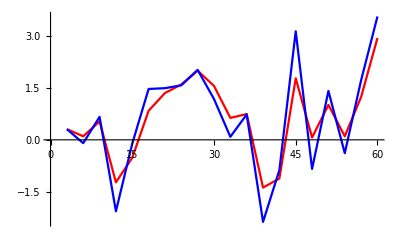

```mathematica
gtable=Table[{3 n,RandomVariate[NormalDistribution[0,1]]},{n,1,20}];(*generate an uncorrelated normal distribution g*)
rTable=Table[
{3 n,g[3 n-3]*gtable[[1,2]]+
Sqrt[1-f[1]^2] *Sum[f[3 n-3i]*gtable[[i,2]],{i,2,n}]},
{n,1,20}];(*using the trick to generate a time correlated normal distribution r*)
ListLinePlot[{rTable,gtable},PlotStyle->{Red,Blue}]
```

```mathematica
g[m_]:=E^(-m/30);(*tau=10s, time step = 3s*)
```

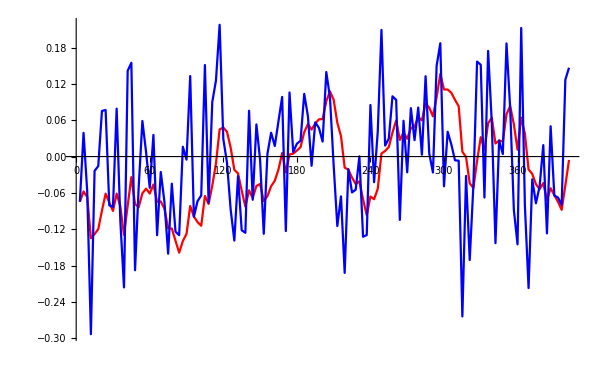

```mathematica
gtable=Table[{3 n,RandomVariate[NormalDistribution[0,toydelomega]]},{n,1,Ceiling[toytf/toytjit]*toytjit/3}];
rTable=Table[
{3 n,g[3 n-3]*gtable[[1,2]]+
Sqrt[1-g[1]^2] *Sum[g[3 n-3i]*gtable[[i,2]],{i,2,n}]},
{n,1,Ceiling[toytf/toytjit]*toytjit/3}];
ListLinePlot[{rTable,gtable},PlotStyle->{Red,Blue}]
```

#### Toy Model x(t)

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {(-1.15032×10^-9-1.53571×10^-9 ⅈ)[y] (1+Piecewise[{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«124»},0])^2==Cos[y],True,(-1.15032×10^-9-1.53571×10^-9 ⅈ)[0]==0}.

NDSolve::dsvar: 0.00817143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.856299 (-1.15032×10^-9-1.53571×10^-9 ⅈ)[0.00817143]==0.999967,True,(-1.15032×10^-9-1.53571×10^-9 ⅈ)[0]==0},-1.15032×10^-9-1.53571×10^-9 ⅈ,{0.00817143,0,400}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00817143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.856299 (-1.15032×10^-9-1.53571×10^-9 ⅈ)[0.00817143]==0.999967,True,(-1.15032×10^-9-1.53571×10^-9 ⅈ)[0.]==0.},-1.15032×10^-9-1.53571×10^-9 ⅈ,{0.00817143,0.,400.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 8.17144 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0.870976 (-1.15032×10^-9-1.53571×10^-9 ⅈ)[8.17144]==-0.31215,True,(-1.15032×10^-9-1.53571×10^-9 ⅈ)[0]==0},-1.15032×10^-9-1.53571×10^-9 ⅈ,{8.17144,0,400}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

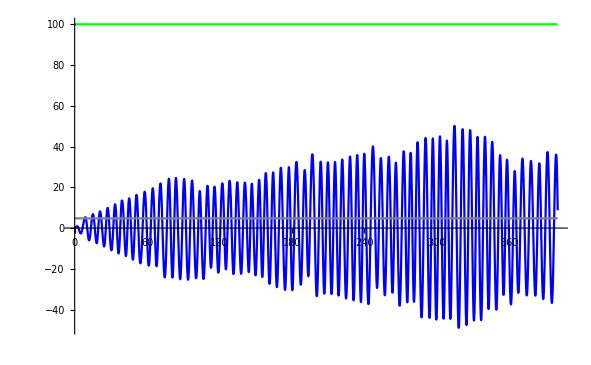

```mathematica
jitterdata=Table[{x,RandomVariate[NormalDistribution[0,toydelomega]]},{x,toytjit,Ceiling[toytf/toytjit]*toytjit,toytjit}];
jitter=Table[{jitterdata[[i,2]],y<jitterdata[[i,1]]},{i,1,Length[jitterdata]}];
solUC=NDSolve[{z''[y]+2 toygamma*z'[y]+(toyomega0+Piecewise[jitter])^2*z[y]==F*Cos[toyomegaF*y],z'[0]==dx0,z[0]==x0},z,{y,0,toytf}];
Rjitter=Table[{rTable[[i,2]],y<rTable[[i,1]]},{i,1,Length[rTable]}];
sol=NDSolve[{x''[y]+2 toygamma*x'[y]+(toyomega0+Piecewise[Rjitter])^2*x[y]==F*Cos[toyomegaF*y],x'[0]==dx0,x[0]==x0},x,{y,0,toytf}];
Plot[{x[y]/.sol,z[y]/.solUC,F/Sqrt[toygamma^2*toyomegaF^2],F/Sqrt[((toyomega0+toydelomega)^2-toyomegaF^2)^2+toygamma^2*toyomegaF^2]},{y,0,toytf},PlotStyle->{Red,Blue,Green,Gray}]
```

## Real Model

#### Real Model Parameters

```mathematica
omega0=1.3*^9;
delomega=4;
gamma=0.4;
F0=1;
m=1;
```

#### Integrated Functions

```mathematica
xf[x0_,v0_,delomega_,t_,t0_]:=E^(-gamma*t/2)*(x0*Cos[(omega0+delomega)*t]+v0/(omega0+delomega)*Sin[(omega0+delomega)*t])+F0*E^(-I*omega0*(t+t0))/m/omega0/(2*delomega-I*gamma)*(1-E^(-gamma*t/2-I*delomega*t));
vf[x0_,v0_,delomega_,t_,t0_]:=E^(-gamma*t/2)*(-(omega0+delomega)*x0*Sin[(omega0+delomega)*t]+v0*Cos[(omega0+delomega)*t])-I*F0*E^(-I*omega0*(t+t0))/m/(2*delomega-I*gamma)*(1-E^(-gamma*t/2-I*delomega*t));
yf[x0_,v0_,delomega_,t_,t0_]:=xf[x0,v0,delomega,t,t0]+I*vf[x0,v0,delomega,t,t0]/omega0;
```

```mathematica
num=10000;
g[m_]:=E^(-m/10);(*correlation scale=10*time step=tau*)
```

```mathematica
gtable=Table[{n,RandomVariate[NormalDistribution[0,delomega]]},{n,1,num}];
rtable=Table[
g[n-1]*gtable[[1,2]]+
Sqrt[1-g[1]^2] *Sum[g[n-i]*gtable[[i,2]],{i,2,n}],
{n,1,num}]
```

General::munfl: -7.39739×10^-308+9.52384×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -6.69344×10^-308+8.61752×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -6.05647×10^-308+7.79746×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
t=0.006;(*simluation step, generally one order smaller than tau. now we set tau=0.06s, 60 ms. *)
num=10000;
delomega0=1;
delomegas=rtable;
xs={0};
vs={0};
Do[
x=xs[[-1]];
v=vs[[-1]];
delomega=delomegas[[Length[xs]]];
t0=t*(Length[xs]-1);
AppendTo[xs,xf[x,v,delomega,t,t0]];
AppendTo[vs,vf[x,v,delomega,t,t0]];,num]
```

```mathematica
delomegasd=RandomVariate[NormalDistribution[0,delomega0],num]
```

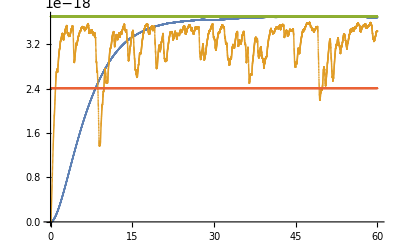

```mathematica
ListPlot[{Table[{t*(i-1),Abs[xs[[i]]]^2},{i,1,Length[xs]}],Table[{t*(i-1),Abs[xsd[[i]]]^2},{i,1,Length[xsd]}],Table[{t*(i-1),Abs[F0]^2/m^2/omega0^2/gamma^2},{i,1,Length[xs]}],Table[{t*(i-1),Abs[F0]^2/m^2/(omega0^2 (gamma+4^2*6*10^(-3))^2)},{i,1,Length[xs]}]}]
```

```mathematica
t=0.06;(*simluation step, generally one order smaller than tau. now we set tau=0.06s, 60 ms. *)
num=10000;
delomega0=1;
delomegasd;
xsd={0};
vsd={0};
Do[
xd=xsd[[-1]];
vd=vsd[[-1]];
delomegad=delomegasd[[Length[xsd]]];
t0=t*(Length[xsd]-1);
AppendTo[xsd,xf[xd,vd,delomegad,t,t0]];
AppendTo[vsd,vf[xd,vd,delomegad,t,t0]];,num]
```

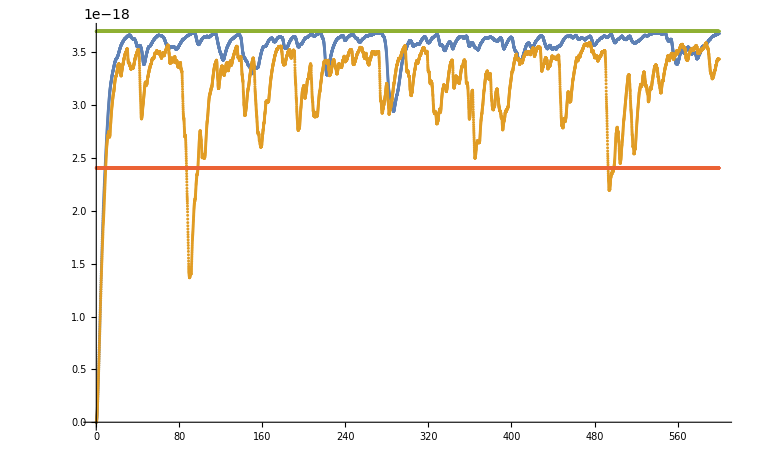

```mathematica
ListPlot[{Table[{t*(i-1),Abs[xs[[i]]]^2},{i,1,Length[xs]}],Table[{t*(i-1),Abs[xsd[[i]]]^2},{i,1,Length[xsd]}],Table[{t*(i-1),Abs[F0]^2/m^2/omega0^2/gamma^2},{i,1,Length[xs]}],Table[{t*(i-1),Abs[F0]^2/m^2/(omega0^2 (gamma+4^2*6*10^(-3))^2)},{i,1,Length[xs]}]}]
```

## Others...

```mathematica
t=0.03;
num=50000;
delomega0=1;
delomegas=RandomVariate[NormalDistribution[0,delomega0],num];
xs={0};
vs={0};
Do[
x=xs[[-1]];
v=vs[[-1]];
delomega=delomegas[[Length[xs]]];
t0=t*(Length[xs]-1);
AppendTo[xs,xf[x,v,delomega,t,t0]];
AppendTo[vs,vf[x,v,delomega,t,t0]];,num]
```

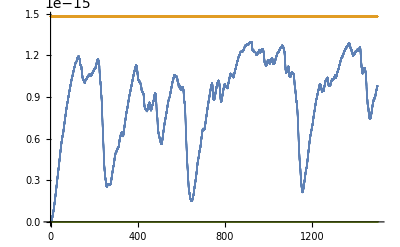

```mathematica
ListPlot[{Table[{t*(i-1),Abs[xs[[i]]+I*vs[[i]]/omega0]^2},{i,1,Length[xs]}],Table[{t*(i-1),4*Abs[F0]^2/m^2/omega0^2/gamma^2},{i,1,Length[xs]}],Table[{t*(i-1),Abs[F0]^2/m^2/omega0^2/gamma*t},{i,1,Length[xs]}]}]
```

```mathematica
n=6000;
x0=xs[[n]];
v0=vs[[n]];
delomega0=delomegas[[n]];
t0=t*(n-1);
y0=x0+I*v0/omega0//N
yf[x0,v0,delomega0,t,t0]
Abs[yf[x0,v0,delomega0,t,t0]]^2-Abs[y0]^2
(2/m/omega0*Im[Conjugate[F0]*y0*E^(I*omega0*t0)]-gamma*Abs[y0]^2)*t+Abs[F0]^2/m^2/omega0^2*t^2
{2/m/omega0*Im[Conjugate[F0]*y0*E^(I*omega0*t0)]*t,-gamma*Abs[y0]^2*t,Abs[F0]^2/m^2/omega0^2*t^2}
```

-2.82775×10^-8-1.0976×10^-8 ⅈ

5.71254×10^-9-2.97947×10^-8 ⅈ

2.66264×10^-19

2.68465×10^-19

{1.37204×10^-18,-1.10411×10^-18,5.32544×10^-22}

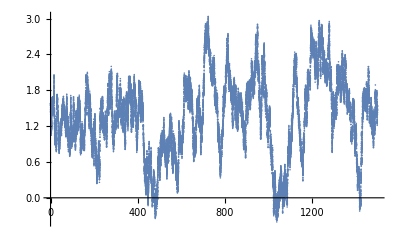

```mathematica
ListPlot[Table[{t*(i-1),Arg[Conjugate[F0]*(xs[[i]]+I*vs[[i]]/omega0)*E^(I*omega0*t*(i-1))]},{i,1,Length[xs]}]]
```

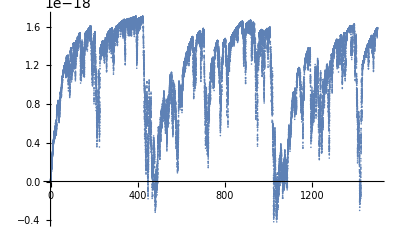

```mathematica
ListPlot[Table[{t*(i-1),2/m/omega0*Im[Conjugate[F0]*(xs[[i]]+I*vs[[i]]/omega0)*E^(I*omega0*t*(i-1))]*t},{i,1,Length[xs]}]]
```